# Plotting the thermal power spectrum of a harmonic oscillator

```mathematica
Clear[f]
psd[f_]=Sqrt[2*kB*T/(Pi*f0*k*Q)*1/((1-(f/f0)^2)^2+(f/(f0*Q))^2)]
```

√(2/π) √((kB T)/(f0 k ((1-f^2/f0^2)^2+f^2/(f0^2 Q^2)) Q))

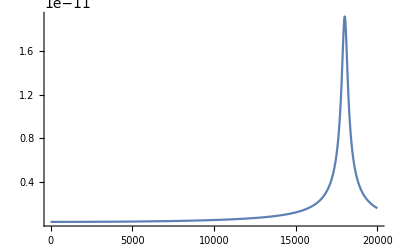

```mathematica
Q=50;
k=0.02;
f0=18000;
kB=1.38*10^-23;
T=300;

Plot[psd[f],{f,0,20000},PlotRange->All]
```